# Isosceles Triangle

### Author

Eric W. Weisstein
July 23, 2014

This notebook downloaded from http://mathworld.wolfram.com/notebooks/Triangles/IsoscelesTriangle.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/IsoscelesTriangle.html.

©2014 Wolfram Research, Inc. except for portions noted otherwise

## Definitions

```mathematica
ineq=-a/2≤x≤a/2&&0≤y≤(1-Abs[x/(a/2)]) h;
```

```mathematica
implreg=ImplicitRegion[ineq,{x,y}];
```

```mathematica
reg=Triangle[{{-a/2,0},{a/2,0},{0,h}}];
```

```mathematica
assum=a>0&&h>0;
```

```mathematica
t=Triangle[{{-𝒶/2,0},{𝒶/2,0},{0,h}}]
```

Triangle[{{-𝒶/2,0},{𝒶/2,0},{0,h}}]

## Figure

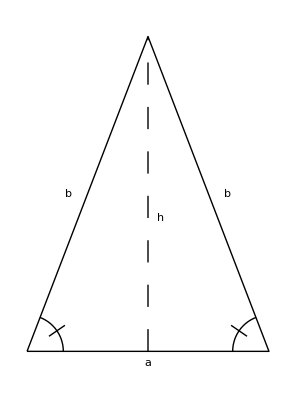

```mathematica
With[{a=1,h=1.3},Graphics[{
Line[v={{-a/2,0},{a/2,0},{0,h},{-a/2,0}}],
{Dashing[.04],Line[{{0,0},{0,h}}]},
EqualAngleTicks[v[[#]],1,.15,.04,1]&/@{{3,1,2},{1,2,3}},
Text[Style["a",Italic],{0,-.05}],
Text[Style["b",Italic],#]&/@{{-.33,.65},{.33,.65}},
Text[Style["h",Italic],{.05,h/2-.1}]
}]]
```

## Plots

### Diagram

```mathematica
Show[LaminaData["FilledIsoscelesTriangle","Diagram"],Axes->False]
```

-Graphics-

### DiscretizeRegion

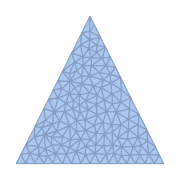

```mathematica
Block[{a=1, h=1},Show[DiscretizeRegion[reg],ImageSize->Small]]
```

### RegionPlot

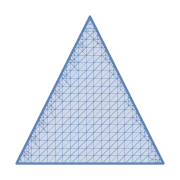

```mathematica
Block[{a=1,h=1},RegionPlot[ineq,{x,-a/2,a/2},{y,0,h},AspectRatio->Automatic,ImageSize->Small,Frame->False]]
```

### InequalityPlot

```mathematica
<<Graphics`InequalityGraphics`
```

```mathematica
With[{a=1,h=2},InequalityPlot[-a/2<x<a/2&&0<y<(1-Abs[x/(a/2)])h,{x},{y},Ticks->None]]
```

⁃Graphics⁃

## Equations

### Inequality

```mathematica
ineq[x_,y_]:=-a/2<x<a/2&&0<y<(1-Abs[x/(a/2)])h
```

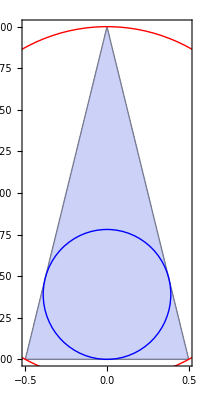

```mathematica
Block[{a=1,h=2},
Show[{
RegionPlot[ineq[x,y],{x,-a/2,a/2},{y,0,h},AspectRatio->Automatic],
Graphics[{Blue,inc,Red,circumc}]
}]
]
```

## Properties

### Area

#### Area

```mathematica
Assuming[assum,Simplify@Area[reg]]
```

(a h)/2

#### Integrate

```mathematica
Integrate[Boole[-a/2<x<a/2&&0<y<(1-Abs[x/(a/2)])h],{x,-∞,∞},{y,-∞,∞},Assumptions->a>0&&h>0]
```

(a h)/2

```mathematica
Assuming[a>0&&h>0,Area[-a/2≤x≤a/2&&0≤y≤(1-Abs[x/(a/2)]) h,{x,y}]]
```

(a h)/2

```mathematica
Integrate[Boole[ineq[x,y]],{x,-∞,∞},{y,-∞,∞},Assumptions->a>0&&h>0]
```

(a h)/2

#### RegionMeasure

```mathematica
Assuming[assum,Simplify@RegionMeasure[reg]]
```

(a h)/2

### Centroid

#### Integrate

```mathematica
Assuming[a>0&&h>0,Centroid[-a/2≤x≤a/2&&0≤y≤(1-Abs[x/(a/2)]) h,{x,y}]]
```

{0,h/3}

```mathematica
Integrate[{x,y}Boole[ineq[x,y]],{x,-∞,∞},{y,-∞,∞},Assumptions->a>0&&h>0]
```

{0,(a h^2)/6}

```mathematica
%/((a h)/2)
```

{0,h/3}

#### RegionCentroid

```mathematica
Assuming[assum,Simplify@RegionCentroid[reg]]
```

{0,h/3}

### SideLengths

```mathematica
abc=Simplify[SideLengths[Evaluate[t]],𝒶>0&&h>0]/.𝒶->a
```

{√(a^2/4+h^2),√(a^2/4+h^2),a}

### Incircle

```mathematica
inc=FullSimplify[Incircle[t],𝒶>0&&h>0]/.𝒶->a
```

Circle[{0,(a h)/(a+√(a^2+4 h^2))},(a √(a^2+2 h^2-a √(a^2+4 h^2)))/(2 √2 h)]

### Circumcircle

```mathematica
circumc=FullSimplify[Circumcircle[t],𝒶>0&&h>0]/.𝒶->a
```

Circle[{0,-a^2/(8 h)+h/2},1/8 (a^2/h+4 h)]

### InertiaTensor

```mathematica
Integrate[AreaInertiaTensor[{x,y}]Boole[ineq[x,y]],{x,-∞,∞},{y,-∞,∞},Assumptions->a>0&&h>0]
```

{{(a h^3)/12,0},{0,(a^3 h)/48}}

### RadiiOfGyration

```mathematica
Assuming[a>0&&h>0,FullSimplify[RadiiOfGyration[ineq[x,y],{x,y}]]]
```

{h/(√6),a/(2 √6)}

## Erecting Isosceles Triangles on Arbitrary Triangle

```mathematica
tri={{0,0},{1,0},{.4,.7}};

Show[Graphics[{
{Thickness[.012],Triangle[tri]},
RGBColor[0,0,1],e=ErectScaleneTriangles[tri,.5],
RGBColor[1,0,0],
Line/@(l=Transpose[{v=Last@@@e,tri}]),
PointSize[.03],Point[LineLineIntersection@@Take[l,2]],
RGBColor[0,0,1],PointLabels[Flatten[Transpose[{v,{"A'","B'","C'"}}],1],.03,.04],
Dashing[{.02,.02}],Triangle[v],
RGBColor[0,0,0],
PointLabels[Flatten[Transpose[{tri,{"A","B","C"}}],1],.03,.04]
}/.Triangle:>polygon,AspectRatio->Automatic],PlotRange->All]
```

⁃Graphics⁃

```mathematica
PerspectiveQ[tri,v]
```

True

```mathematica
CollinearQ@PerspectiveAxis[tri,v]
```

True